# QNM Computation and Sequential Storage

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* Schwarzschild: vedere dipendenza da infinito al variare dell'ordine dell'espansione. Vedere andamento fissando uno/due parametri. Eventualmente ampliare volume esplorato *)
(* Kerr: vedere che succede con molti punti. Obiettivo futuro: variare spin e quindi qnm *)
(* ECO: per ora in pausa (vedere cosa risultati del resto) *)
```

```mathematica
(* Esplorare Kerr a spin 0 in eps, match e inf così da fare confronto con Schw *)
```

### Tests

```mathematica
Tuples[{x,y}];Flatten[ECO[[;;]],1]//N;
```

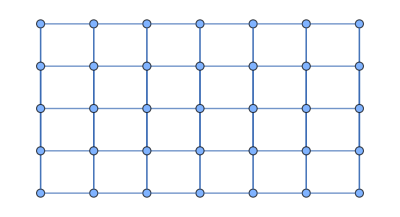

```mathematica
g=NearestNeighborGraph[Tuples[{x[[;;7]],y[[;;5]]}],{All,1/5},DistanceFunction->ManhattanDistance,GraphLayout->"BipartiteEmbedding"]
```

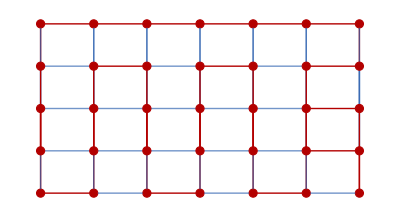

```mathematica
HighlightGraph[g,PathGraph[FindHamiltonianCycle[g,1][[1]]]]
```

```mathematica
-Graphics-//EdgeList
```

{1<->2,1<->4,2<->3,2<->5,3<->6,4<->5,4<->7,5<->6,5<->8,6<->9,7<->8,7<->10,8<->9,8<->11,9<->12,10<->11,11<->12}

```mathematica
g//EdgeList
```

{{1/8,10}<->{1/8,99/10},{1/8,10}<->{1/8,49/5},{1/8,10}<->{1/4,10},{1/8,99/10}<->{1/8,49/5},{1/8,99/10}<->{1/4,99/10},{1/8,49/5}<->{1/4,49/5},{1/4,10}<->{1/4,99/10},{1/4,10}<->{1/4,49/5},{1/4,10}<->{3/8,10},{1/4,99/10}<->{1/4,49/5},{1/4,99/10}<->{3/8,99/10},{1/4,49/5}<->{3/8,49/5},{3/8,10}<->{3/8,99/10},{3/8,10}<->{3/8,49/5},{3/8,10}<->{1/2,10},{3/8,99/10}<->{3/8,49/5},{3/8,99/10}<->{1/2,99/10},{3/8,49/5}<->{1/2,49/5},{1/2,10}<->{1/2,99/10},{1/2,10}<->{1/2,49/5},{1/2,99/10}<->{1/2,49/5}}

```mathematica
FindHamiltonianCycle[-Graphics-];
```

```mathematica
HighlightGraph[-Graphics-,First[]]
```

-Graphics-

## QNM Finder

We adopt a direct integration method to find the first quasi-normal mode (QNM) of a specific compact object (CO).

First, the perturbation equation is numerically integrated from the horizon (surface in the case of an ECO) to the outside and from infinity to the inside. The two solutions are “attached together” at a point of match. The QNM is estimated as the value smoothing the solution. This is done searching for a continuous derivative, i.e. requesting zero deviation between the left and right side when evaluated at the point of match.

In this Chapter the implementation is generalized to accept any perturbation equation (e.g. Regge-Wheeler or Teukolsky) and boundary condition. Two functions are defined:
	- IntQNM: performs direct integration of the perturbation equation at fixed ω, returns the deviation of the first derivate;
	- FindQNM: searches the root of IntQNM.

```mathematica
(* BC set-up archetype *)
SchwBC[coefI_,coefE_]:=Module[{ordI,bcI,ordE,bcE},
ordI=Length[coefI];bcI=Exp[-ⅈ ω rs[r]]Sum[hHor[i](r-2M)^i,{i,0,ordI}]//.coefI;
ordE=Length[coefE];bcE=Exp[ⅈ ω rs[r]]Sum[gInf[i] r^-i,{i,0,ordE}]//.coefE;

Return[{bcI,bcE}];
];
KerrBC[coefI_,coefE_]:=Module[{ordI,bcI,ordE,bcE},
ordI=Length[coefI];bcI=Exp[-ⅈ k rs[r]] Δ[r]^(-s/2)Sum[hHor[i](r-rp)^i,{i,0,ordI}]//.coefI;
ordE=Length[coefE];bcE=Exp[ⅈ ω rs[r]] r^-s Sum[gInf[i] r^-i,{i,0,ordE}]//.coefE;

Return[{bcI,bcE}];
];
```

```mathematica
(* --- Integrator --- *)
(* NOTE: *)
(* eq_    : perturbation equation - the unknown's name must be ψ *)
(* par_   : list of rules for the CO parameters (e.g. mass, spin, etc.) - names depends on the definition of eq_ *)
(* theta_ : list of rules for the integration parameters (eps, match and inf) *)
(* BCs_   : list of two expressions depending on r and the CO *)
(* In principle par_ and theta_ can be substituted by a single list of rules. 
Although, this distinction allows to more easily separate fixed parameters and variables during a parameter space exploration (see below). 
Here we leave to lists for consistency and to pass them without manipulations of sort *)
IntQNM[ω0_,eq_,par_,theta_,BCs_]:=Module[{rules,param,prec,rI,rM,rE,ξ,ξI,ξE,EQ,BC,b,Δξp},
rules={AccuracyGoal->12,PrecisionGoal->12,WorkingPrecision->20};

param=Union[{ω->ω0},par,theta];
prec=Max[20,Precision[param]];param=SetPrecision[param,prec];

rI=2M(1+eps)/.param;
rM=match M/.param;
rE=inf M/.param;

(* The unknown function's name is standardized to ψ *)
EQ=SetPrecision[{eq==0}//.Union[param,{ψ[r]->ξ[r],ψ'[r]->ξ'[r],ψ''[r]->ξ''[r]}],prec];

(* Solution integrating from the horizon *)
BC=SetPrecision[{ξ[rI]==BCs[[1]],ξ'[rI]==D[BCs[[1]],r]}//.Union[{r->rI},param],prec];
ξI=ξ[r]/.NDSolve[Union[EQ,BC],ξ,{r,rI,rM},rules][[1]];

(* Solution integration from infinity *)
BC=SetPrecision[{ξ[rE]==BCs[[2]],ξ'[rE]==D[BCs[[2]],r]}//.Union[{r->rE},param],prec];
ξE=ξ[r]/.NDSolve[Union[EQ,BC],ξ,{r,rE,rM},rules][[1]];

(*Linear combination*)
b=ξI/ξE/.r->rM;(* we fix the coefficients of the linear combination in order for ψn to be continuous at r=rm *)
(*Υn=Piecewise[{{Υhor,r<rm},{b×Υinf,r≥rm}}];*)
Δξp=(D[ξI,r]-D[b ξE,r])/D[ξI,r]/.r->rM;
Return[Δξp];
];
```

```mathematica
(* --- Finder archetype --- *)
(* NOTE: *)
(* ωguess_ : initial guess given to FindRoot *)
(* par_ and theta_ are the same of IntQNM *)
(* EQ and BC are set outside for the specific CO *)
FindQNM[ω0_,par_,theta_]:=Module[{g,ωroot,rules},
rules={AccuracyGoal->6,WorkingPrecision->20};
g[x_?NumericQ]:=IntQNM[x,EQ,par,theta,BC];
ωroot=x/.FindRoot[g[x]==0,{x,ω0},AccuracyGoal->6,WorkingPrecision->20(*,EvaluationMonitor:>Print["ω = ", x," Δψ' = ",Abs[g[x]]]*)][[1]];
Return[{ωroot,Abs[g[ωroot]]}];
];
```

## Grid Search

In this Chapter the hyperparameter space is explored along a grid. This approach grants a relatively rigorous search over the selected volume, hence allowing the study of chosen combinations of parameters.

Multiple functions are defined:
	- RunLine: run FindQNM (see previous Chapter)  over a 1D list of parameters sets, i.e. {{p1, q1,...},{p2,q2,...},...};
	- GridSearchECO: run RunLine over a 2D parameter grid;
	- GridSearch: simple exploration over a grid where ω_guess is fixed (hence most parameters defining the CO as well).

```mathematica
(* --- RunLine --- *)
(* NOTE: *)
(* par_    : list of rules setting any fixed parameter of the computation *)
(* fun_    : function setting the substitution rules (allows to choose which parameters to change) *)
(* points_ = {{p1,q1,...},{p2,q2,...},...} *)
RunLine[ω0_,par_,fun_,points_]:=Module[{ωguess=ω0},
Map[With[{r=Join[#,FindQNM[ωguess,par,fun[#]]]},ωguess=r[[3]];r]&,points]
];
```

```mathematica
(* --- GridSearchECO --- *)
(* NOTE: *)
(* par_    : list of rules setting any fixed parameter of the computation *)
(* fun_    : function setting the substitution rules (allows to choose which parameters to change) *)
(* ranges_ = {{{start, end, step},{...},...},{...}} sets the grid values *)
GridSearchECO[ω0_,par_,fun_,ranges_]:=Module[{ai,aj,row1,cols,n,i=0},
{ai,aj}=Union@@@Map[Range@@#&,ranges,{2}];n=Times@@Length/@{ai,aj};(* grid values in each dimensions *)
DistributeDefinitions[RunLine,FindQNM];SetSharedVariable[i];(* definitions to run parallel computations *)

row1=RunLine[ω0,par,fun,Thread[{First[aj],ai}]];(* j=1 is fixed and runs over i *)
cols=Monitor[ParallelMap[
With[{c=Prepend[RunLine[#[[3]],par,fun,Thread[{Rest[aj],#[[2]]}]],#]},
i++;c]&,row1,Method->"FinestGrained"],
Row[{ProgressIndicator[i,{0,n}]," ",i,"/",n}]];(* runs over j in parallel for every i *)
Return[cols//Transpose];
];
```

```mathematica
(* --- GridSearch --- *)
(* NOTE: *)
(* par_    : list of rules setting any fixed parameter of the computation *)
(* fun_    : function setting the substitution rules (allows to choose which parameters to change) *)
(* ranges_ = {{{start, end, step},{...},...},{...}} sets the grid values *)
GridSearch[ω0_,par_,fun_,ranges_]:=Module[{axis,data,dims,n,i=0},
axis=Union@@@Map[Range@@#&,ranges,{2}];
dims=Length/@axis;n=Times@@dims;
data=Monitor[ParallelMap[
With[{r=FindQNM[ω0,par,fun[#]]},i++;Join[#,r]]&,Tuples[axis],Method->"FinestGrained"],
Row[{ProgressIndicator[i,{0,n}]," ",i,"/",n}]];
Return[Fold[Partition,data,Reverse@Rest@dims]];
];
```

### test

```mathematica
ωSBH=(0.7473433688360838`20- 0.1779246313778714`20ⅈ)/2
```

0.3736716844180419-0.0889623156889357 ⅈ

```mathematica
EQ=EQRW;BC=EcoBC[{},coefInf];
IntQNM[2/5-ⅈ/10,EQ,{M->1,l->2,match->10,inf->50,gInf[0]->1},{η->1/(16π),eps->10^-10},BC]
```

-0.0718364303327564-0.031188999285969 ⅈ

```mathematica
FindQNM[2/5-ⅈ/10,{M->1,l->2,match->10,inf->50,gInf[0]->1},{η->1/(16π),eps->10^-10}]
```

{0.37367157521106630403-0.088962318604243888456 ⅈ,5.×10^-16}

```mathematica
RunLine[2/5-ⅈ/10,{M->1,l->2,match->10,inf->50,gInf[0]->1},SubsHE,{{1/(16π),10^-10},{1/(16π),10^-8},{1/(16π),10^-6}}]
```

{{1/(16 π),1/10000000000,0.37367157521106630403-0.088962318604243888456 ⅈ,5.×10^-16},{1/(16 π),1/100000000,0.37366988708608859291-0.088962084470769466367 ⅈ,0.},{1/(16 π),1/1000000,0.37364545364126550841-0.088939811003950703958 ⅈ,7.32×10^-14}}

```mathematica
GridSearchECO[2/5-ⅈ/10,{M->1,l->2,match->10,inf->50,gInf[0]->1},{{{1/(32π),1/(16π),1/(32π)}},{{10^-4,10^-3,5 10^-4}}},SubsHE]
```

{{{1/10000,1/(32 π),0.42866517234187922285-0.21527838170601877008 ⅈ,8.3585×10^-12},{1/10000,1/(16 π),0.42800792722451602074-0.21549690428817031874 ⅈ,1.03×10^-13}},{{3/5000,1/(32 π),0.42866301667922561782-0.21525728997930049298 ⅈ,1.89×10^-13},{3/5000,1/(16 π),0.42797290570114782504-0.21548920511941647222 ⅈ,6.198×10^-13}}}

```mathematica
MatrixForm[%]
```

((1/10000
1/(32 π)
0.42866517234187922285-0.21527838170601877008 ⅈ
8.3585×10^-12) | (1/10000
1/(16 π)
0.42800792722451602074-0.21549690428817031874 ⅈ
1.03×10^-13)
(3/5000
1/(32 π)
0.42866301667922561782-0.21525728997930049298 ⅈ
1.89×10^-13) | (3/5000
1/(16 π)
0.42797290570114782504-0.21548920511941647222 ⅈ
6.198×10^-13))

## ECO

### Parameters

```mathematica
x={};step={{1/8,2-1/8,1/8},{2+1/4,10,1/4},{2,2+1/5,1/20}};
Do[x=Union[x,Table[j,{j,i[[1]],i[[2]],i[[3]]}]],{i,step}];
x=Sort[x];ηarray=(1-10^-x)/(16π);(* x = -Subscript[log, 10][η'] *)
```

```mathematica
y={};step={{6+1/8,8,1/8}};
Do[y=Union[y,Table[j,{j,i[[1]],i[[2]],i[[3]]}]],{i,step}];
y=ReverseSort[y];ϵarray=10^-y;
```

```mathematica
ECO=Table[{h,e},{h,ηarray},{e,ϵarray}];
Print["N = ",Length[ηarray]," η_in = ",ηarray[[1]]//N," η_fin = ",ηarray[[-1]]//N ];
Print["N = ",Length[ϵarray]," ϵ_in = ",ϵarray[[1]]," ϵ_fin = ",ϵarray[[-1]] ];
```

N = 52 η_in = 0.0049757 η_fin = 0.0198944

N = 16 ϵ_in = 1/100000000 ϵ_fin = 1/(1000000 10^(1/8))

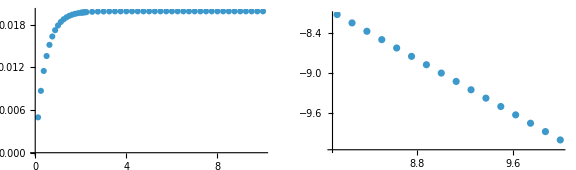

```mathematica
P1=ListPlot[Transpose[{x,ηarray}],PlotRange->All];
P2=ListPlot[Transpose[{y,ϵarray}],PlotRange->All,ScalingFunctions->"Log10"];
GraphicsGrid[{{P1,P2}},ImageSize->Large]
```

### Computation

“QNM_ECO1_heoc_9.m”: running over η.
“QNM_ECO1_heoc_10.m”: running over ϵ.
“QNM_ECO1_heoc_35.m”: running upward (1) over ϵ (+2), then upward (1) over η, adding η (+4). 
“QNM_ECO1_heoc_34.m”: running upward (1) over ϵ (+2), then downward (0) over η, adding η (+4).
“QNM_ECO1_heoc_52.m”

Legenda  per numerazione output (da file 3):
	- ϵ in prima posizione, η in seconda;
	- su quale si itera prima +2;
	- da minore a maggiore +1, viceversa +0;
	- quale si aggiunge nelle run successive +4.
	
Legenda opzioni calcolo (opt):
	1. si aggiungono nuovi valori di ϵ;
	2. si aggiungono nuovi valori di η;
	3. si itera prima su  ϵ;
	4. default (tutte false): nuovo file e si itera prima su η.

```mathematica
opt={True,False,False};
new=Table[{},{i,ηarray},{j,ϵarray}];
```

```mathematica
Which[
opt[[1]],in=Import["QNM_ECO1_heoc_53.m"];ωguess=in[[1,-1,3]](* same ηs and adding ϵs *),
opt[[2]],in=Import["QNM_ECO1_heoc_34.m"];ωguess=in[[-1,1,3]](* same ϵs and adding ηs *),
True,ωguess=(*2/5-1/10 ⅈ*)0.41029219691343865755656481837481117539`20.-0.01210110293339904243328231521370532767`20. ⅈ;(* default: new run *)];
If[opt[[3]],new=new//Transpose;ECO=ECO//Transpose(* running over ϵ then η *)];
Print["ω_guess = ",ωguess//N,"\nDim[in]",in//Dimensions,"\tDim[new] = ",new//Dimensions,"\tDim[ECO] = ",ECO//Dimensions];
```

ω_guess = 0.493874-0.0321904 ⅈ
Dim[new] = {52,16,0}	Dim[ECO] = {52,16,2}

```mathematica
(* Default: running over η then ϵ *)
Monitor[Do[Do[new[[j,i]]=Join[ECO[[j,i]],FindQNM[ωguess,ECO[[j,i]]]];
ωguess=new[[j,i,3]],{j,1,Dimensions[ECO][[1]]}];
ωguess=new[[1,i,3]],{i,1,Dimensions[ECO][[2]]}],Row[{"ij = ",{i,j}}]];

new//Dimensions
```

{52,16,4}

```mathematica
If[opt[[3]],new=new//Transpose]; 
Which[
opt[[1]],out=Join[in//Transpose,new//Transpose]//Transpose,
opt[[2]],out=Join[in,new],
True,out=new];
Print["Dim[out] = ",out//Dimensions];
```

Dim[out] = {52,32,4}

```mathematica
Export["QNM_ECO1_heoc_53.m",out];Clear[out];(* ECO1 i.e. non-rotating ECO *)
```

### Plots

```mathematica
(* da sistemare lasciare solo plot generali dell'output. Il resto da trasferire nella sezione dedicata del notebook specifico *)
```

```mathematica
in1=Import["QNM_ECO1_heoc_52.m"];
in2=Import["QNM_ECO1_heoc_53.m"];
Print["Dim[in1] = ", in1//Dimensions,"\tDim[in2] =",in2//Dimensions];
```

Dim[in1] = {52,32,4}	Dim[in2] ={52,32,4}

```mathematica
(* Real and imaginary part as function of η - remeber Extract *)
Roh1=in1[[;;,;;,1;;3;;2]]//Transpose;Roh1[[;;,;;,2]]=Re[Roh1[[;;,;;,2]]];
Ioh1=in1[[;;,;;,1;;3;;2]]//Transpose;Ioh1[[;;,;;,2]]=-Im[Ioh1[[;;,;;,2]]];
ch1=in1[[;;,;;,1;;4;;3]]//Transpose;
(* Real and imaginary part as function of ϵ *)
Roe1=in1[[;;,;;,2;;3]];Roe1[[;;,;;,2]]=Re[Roe1[[;;,;;,2]]];
Ioe1=in1[[;;,;;,2;;3]];Ioe1[[;;,;;,2]]=-Im[Ioe1[[;;,;;,2]]];
ce1=in1[[;;,;;,2;;4;;2]];
```

```mathematica
(* Real and imaginary part as function of η - remeber Extract *)
Roh2=in2[[;;,;;,1;;3;;2]]//Transpose;Roh2[[;;,;;,2]]=Re[Roh2[[;;,;;,2]]];
Ioh2=in2[[;;,;;,1;;3;;2]]//Transpose;Ioh2[[;;,;;,2]]=-Im[Ioh2[[;;,;;,2]]];
ch2=in2[[;;,;;,1;;4;;3]]//Transpose;
(* Real and imaginary part as function of ϵ *)
Roe2=in2[[;;,;;,2;;3]];Roe2[[;;,;;,2]]=Re[Roe2[[;;,;;,2]]];
Ioe2=in2[[;;,;;,2;;3]];Ioe2[[;;,;;,2]]=-Im[Ioe2[[;;,;;,2]]];
ce2=in2[[;;,;;,2;;4;;2]];
```

### Basic plots

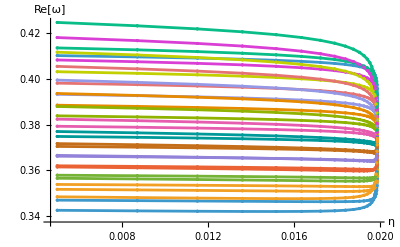

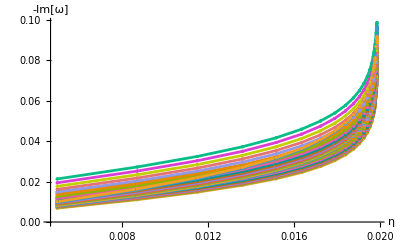

```mathematica
ListPlot[Roh1[[;;]],AxesLabel->{"η","Re[ω]"},ScalingFunctions->{None,None},Joined->True,Mesh->Full,PlotRange->All]
ListPlot[Ioh1[[;;]],AxesLabel->{"η","-Im[ω]"},ScalingFunctions->{None,None},Joined->True,Mesh->Full,PlotRange->All]
(*{{0.0197,0.0199},{0.545,0.5452}}*)
```

```mathematica
in1[[24;;,1,1]]//N
```

{0.0198932,0.0198924,0.0198908,0.0198881,0.0198832,0.0198745,0.019859,0.0198315,0.0197825,0.0197688,0.0197535,0.0197363,0.0197171,0.0196954,0.0196291,0.0195406,0.0194226,0.0192653,0.0190554,0.0187756,0.0184025,0.0179049,0.0172414,0.0163566,0.0151767,0.0136032,0.011505,0.00870694,0.0049757}

```mathematica
1/(16π)//N
```

0.0198944

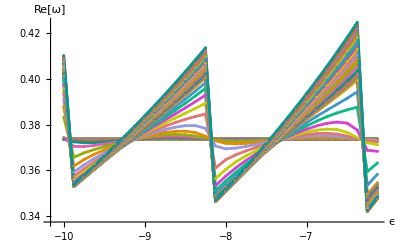

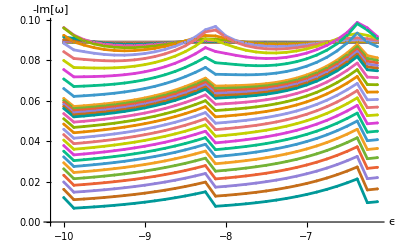

```mathematica
P1=ListPlot[Roe1[[;;,;;]],AxesLabel->{"ϵ","Re[ω]"},ScalingFunctions->{"Log10",None},Joined->True,Mesh->Full,PlotRange->All]
P2=ListPlot[Ioe1[[;;,;;]],AxesLabel->{"ϵ","-Im[ω]"},ScalingFunctions->{"Log10",None},Joined->True,Mesh->Full,PlotRange->All]
(*{{0.0197,0.0199},{0.545,0.5452}}*)
```

```mathematica
Export["ReQNMvEPS_34.jpg",P1];Export["ImQNMvEPS_34.jpg",P2];
```

```mathematica
Export["eta_eps_qnm_eps10-10.m",in1[[;;,1]]];
```

```mathematica
in2[[;;,16,2]]//N
```

{7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9,7.49894×10^-9}

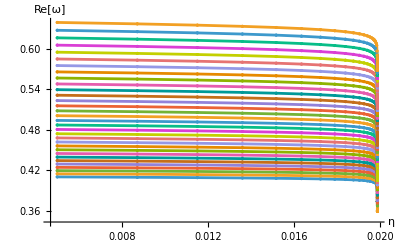

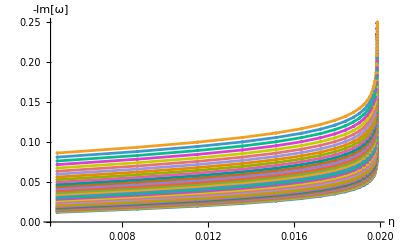

```mathematica
ListPlot[Roh2[[;;]],AxesLabel->{"η","Re[ω]"},ScalingFunctions->{None,None},Joined->True,Mesh->Full,PlotRange->All]
ListPlot[Ioh2[[;;]],AxesLabel->{"η","-Im[ω]"},ScalingFunctions->{None,None},Joined->True,Mesh->Full,PlotRange->All]
(*{{0.0197,0.0199},{0.545,0.5452}}*)
```

```mathematica
in2[[24,1,1]]//N
```

0.0198932

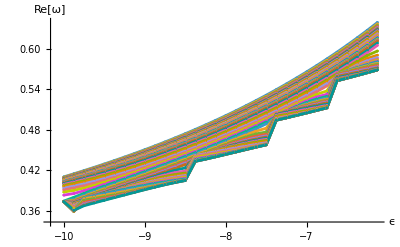

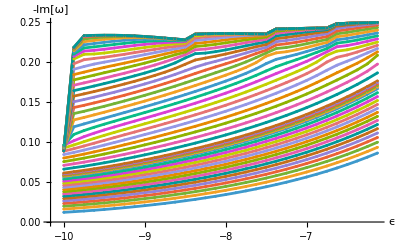

```mathematica
ListPlot[Roe2[[;;]],AxesLabel->{"ϵ","Re[ω]"},ScalingFunctions->{"Log10",None},Joined->True,Mesh->Full,PlotRange->All]
ListPlot[Ioe2[[;;]],AxesLabel->{"ϵ","-Im[ω]"},ScalingFunctions->{"Log10",None},Joined->True,Mesh->Full,PlotRange->All]
(*{{0.0197,0.0199},{0.545,0.5452}}*)
```

### Specific plots

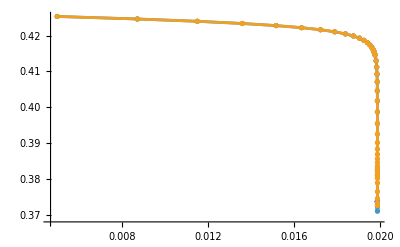

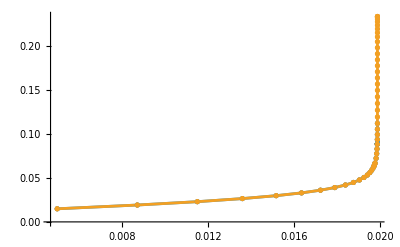

```mathematica
xrange={0.019885,0.019895};index=5;
P1=ListPlot[{Roh2[[index]],Roh1[[index]]},Mesh->Full,Joined->True,Ticks->{xrange, Automatic},PlotRange->{xrange,All}];
P2=ListPlot[{Ioh2[[index]],Ioh1[[index]]},Mesh->Full,Joined->True,Ticks->{xrange,Automatic},PlotRange->{xrange,All}];

ListPlot[{Roh2[[index]],Roh1[[index]]},Mesh->Full,Joined->True,PlotRange->All,Epilog->Inset[P1,Scaled[{0.15,0.15}],Scaled[{0,0}]]]
ListPlot[{Ioh2[[index]],Ioh1[[index]]},Mesh->Full,Joined->True,PlotRange->All,Epilog->Inset[P2,Scaled[{0.15,0.5}],Scaled[{0,0}]]]
(*{{0.01989,0.0199},All}*)
```

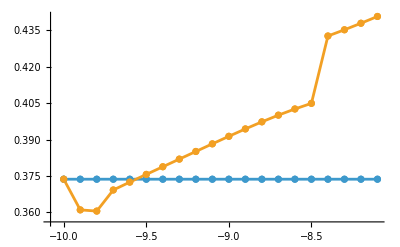

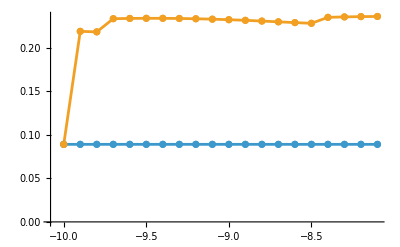

```mathematica
xrange={0.019885,0.019895};
P1=ListPlot[Roe2[[-1,;;20]],ScalingFunctions->{"Log10",None},Mesh->Full,Joined->True,Ticks->{None,Automatic},PlotRange->All];
P2=ListPlot[Ioe2[[-1,;;20]],ScalingFunctions->{"Log10",None},Mesh->Full,Joined->True,Ticks->{None,Automatic},PlotRange->All];

ListPlot[{Roe2[[-1,;;20]],Roe1[[-1]]},ScalingFunctions->{"Log10",None},Mesh->Full,Joined->True,PlotRange->All,Epilog->Inset[P1,Scaled[{0.2,0.6}],Scaled[{0,0}]]]
ListPlot[{Ioe2[[-1,;;20]],Ioe1[[-1]]},ScalingFunctions->{"Log10",None},Mesh->Full,Joined->True,PlotRange->All,Epilog->Inset[P2,Scaled[{0.55,0.45}],Scaled[{0,0}]]]
(*{{0.01989,0.0199},All}*)
```

```mathematica
Roh2//Dimensions
```

{40,52,2}

```mathematica
Roh1//Dimensions
```

{49,24,2}

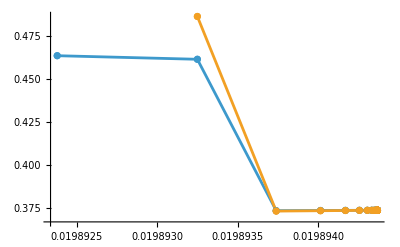

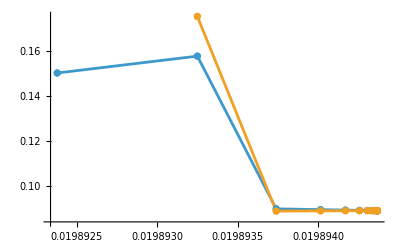

```mathematica
xrange={0.01989,0.019895};index=20;
ListPlot[{Roh2[[index,28;;]],Roh1[[index]]},Mesh->Full,Joined->True,PlotRange->All]
ListPlot[{Ioh2[[index,28;;]],Ioh1[[index]]},Mesh->Full,Joined->True,PlotRange->All]
(*{{0.01989,0.0199},All}*)
```

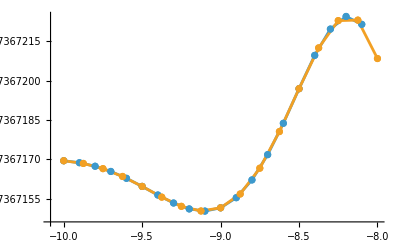

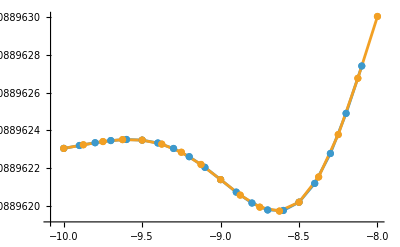

```mathematica
ListPlot[{Roe2[[-1,;;20]],Roe1[[1,;;17]]},ScalingFunctions->{"Log10",None},Mesh->Full,Joined->True,PlotRange->All(*{{Automatic,10^-8},{0.37367,0.373673}}*)]
ListPlot[{Ioe2[[-1,;;20]],Ioe1[[1,;;17]]},ScalingFunctions->{"Log10",None},Mesh->Full,Joined->True,PlotRange->All(*{{Automatic,10^-8},{0.08896,0.08897}}*)]
```

## Kerr

### Spin

```mathematica
χarray={10^-2,5 10^-2,10^-1,15 10^-2,2 10^-1,25 10^-2,3 10^-1};
ωtrue={0.3749365685-0.08894183057ⅈ,0.3801455748-0.08884890191ⅈ,0.3870175384-0.08870569903ⅈ,0.3943329877-0.08852826817ⅈ,0.4021453242-0.08831116621ⅈ,0.4105179098-0.08804765025ⅈ,0.4195266818-0.08772927189ⅈ};
(*ωguess={};*)
```

### Computation

```mathematica
ωfound=Table[{},{i,χarray}];ωguess=0.4-0.1 ⅈ;
Monitor[Do[ωfound[[i]]={χarray[[i]],ωtrue[[i]],FindQNM[ωguess,χarray[[i]]][[1]]};ωguess=ωfound[[i,-1]],
{i,1,Length[χarray]}],Row["Iteration: i = ",i]];
```

```mathematica
Export["QNM_Kerr_generale.m",ωfound]
```

QNM_Kerr_generale.dat

```mathematica
(* con ordHor=3
1.403173173208927*^-7-2.594252477838843*^-7 ⅈ,1.3839418633310174*^-7-2.5434630081255793*^-7 ⅈ,1.305543594343206*^-7-2.399207012504512*^-7 ⅈ *)
```

```mathematica
(* con ordHor=7
1.403173173208927*^-7-2.594252477838843*^-7 ⅈ,1.3839418633310174*^-7-2.5434630081255793*^-7 ⅈ,1.305543594343206*^-7-2.399207012504512*^-7 ⅈ *)
```

## Old stuff

```mathematica
GridSearch[par_,steps_]:=Module[{axis,data,i},
axis=Table[Union@@Table[Table[k,{k,j[[1]],j[[2]],j[[3]]}],{j,i}],{i,steps}];i=0;
data=Monitor[Outer[i++;Join[{##},FindQNM[par[[1]],{##},par[[2]]]]&,Sequence@@axis],Row[{"Iteration: i = ",i}]];
Return[data];
];
```

```mathematica
steps={{{1,5,1}},{{1,10,2}}};
axis=Union@@@Map[Range@@#&,steps,{2}];i=0;
data=Monitor[i++;Join[{##},Exp[{##}]]&@@@Tuples[axis],Row[{"Iteration: i = ",i}]];
```

```mathematica
dims=Length/@axis;
Fold[Partition,data,Reverse@Rest@dims]//MatrixForm
```

```mathematica
Output[par_,theta_]:=Module[{data},
data=FindQNM[];
];
```

```mathematica
{ai,aj}=Union@@@Map[Range@@#&,{{{1,5,1}},{{1,10,2}}},{2}];
DistributeDefinitions[RunLine,fun];
par={0,0};
Print[Thread[{First[aj],ai}]];
row1=RunLine[par[[1]],par[[2]],Thread[{First[aj],ai}]];        (*j=1,sequenziale su i*)
cols=ParallelMap[Prepend[RunLine[#[[3]],par[[2]],Thread[{Rest[aj],#[[2]]}]],#]&,row1,Method->"FinestGrained"];
```

{{1,1},{1,2},{1,3},{1,4},{1,5}}

```mathematica
points=Tuples[arrays];
total=Length[points];
count=0;current=None;
SetSharedVariable[count,current];

flat=Monitor[ParallelMap[With[{r=f[p1,p2,#]},count++;current=#;Join[#,r]]&,points,Method->"FinestGrained"],Row[{ProgressIndicator[count,{0,total}],"  ",count,"/",total,"   ultimo punto: ",current}]];

res=Fold[Partition,flat,Reverse@Rest@dims];
```

## Random Search

In this Chapter the hyperparameter space is explored randomly. This approach allows for a relatively fast search over the selected volume.
The implementation is the following:
	- RandomSearch: handles sampling, calculation and final output;
	- See above for IntQNM and FindQNM.

```mathematica
(* --- RandomSearch --- *)
(* NOTE: *)
(* par_ = {Subscript[ω, guess], Subscript[ω, true], and list of rules for CO parameters (see IntQNM above)} *)
(* ops_    : functions to set hyperparameters taking as input an uniformly distributed random variable *)
(* ranges_ : ranges of each uniform distribution *)
(* n_      : number of iterations *)
(* output  : {theta, Re[Δω], Im[Δω], Abs[Δω]} where Δω = Subscript[ω, found] - Subscript[ω, true] *)
RandomSearch[par_,ops_,ranges_,n_]:=Module[{data,theta,Δω},
data={};
Monitor[Do[
theta=MapThread[#1[#2]&,{ops,RandomVariate[UniformDistribution[#]]&/@ranges}];
Δω=FindQNM[par[[1]],par[[3]],theta][[1]]-par[[2]];
AppendTo[data,Join[theta,{Re[Δω],Im[Δω],Abs[Δω]}]],{i,n}],Row[{"Iteration: i = ",i}]];
Return[data];
];
```

```mathematica
(* --- RandomSearch V2 --- *)
RandomSearch[par_,ops_,ranges_,n_]:=Module[{data,theta,i=0},
theta=MapThread[#1[#2]&,{{#&,10#&},RandomVariate[UniformDistribution[#],10]&/@ranges}]//Transpose;
data=Monitor[i++;Join[{##},FindQNM[par[[1]],par[[2]],{##}]]&@@@theta,Row[{"Iteration: i = ",i,"/",n}]];
Return[data];
];
```

## Schwarzschild (eps, match, inf)

```mathematica
FindQNM[ωguess_,par_,theta_]:=Module[{g,ωroot},
g[x_?NumericQ]:=IntQNM[x,Join[{2},theta],coefHor,coefInf][[1]];
ωroot=x/.FindRoot[g[x]==0,{x,ωguess},AccuracyGoal->6,WorkingPrecision->20][[1]];

Return[{ωroot,Abs[g[ωroot]]}];
]
```

```mathematica
EQ=EQRW;BC=SchwBC[Import["SeriesCoef\\CoefHor_Schw_10.m"],Import["SeriesCoef\\CoefInf_Schw_10.m"]];
```

```mathematica
ωSBH=(0.7473433688360838- 0.1779246313778714ⅈ)/2;ωguess=2/5-ⅈ/10;
par={l->2,M->1};
(* --- Output File --- *)
(* Name format: *)
(* parameters    : expansion order (horizon-infinty, if equal one is omitted) *)
(* output format : {ϵ, μ, ι, Re[Δω], Im[Δω], Abs[Δω]} *)
(* file numeration (i.e. different run and different hyperparameters) *)
fileName="Schw_10_emidRdIdA_2.m";
```

```mathematica
data=RandomSearch[{ωguess,ωSBH,par},{10^#&,#&,#&},{{-10,-3},{5,10},{60,60}},500];
Print["Dim[data] = ",data//Dimensions];
```

Dim[data] = {500}

```mathematica
(* --- Output File --- *)
Export["Data_RSearch\\"+fileName,data];Clear[data];
```

## Kerr (eps, match, inf)

```mathematica
EQ=EQT;BC=KerrBC[Import["SeriesCoef\\CoefHor_Kerr_4.m"],Import["SeriesCoef\\CoefInf_Kerr_10.m"]];
```

```mathematica
ωSBH=(0.7473433688360838- 0.1779246313778714ⅈ)/2;ωguess=2/5-ⅈ/10;
par={l->2,m->2,s->-2,M->1,χ->0};
(* --- Output File --- *)
(* Name format: *)
(* parameters    : expansion order (horizon-infinty, if equal one is omitted) *)
(* output format : {ϵ, μ, ι, Re[Δω], Im[Δω], Abs[Δω]} *)
(* file numeration (i.e. different run and different hyperparameters) *)
fileName="Kerr_0_4-10_emidRdIdA_1.m";
```

```mathematica
(*{42/100-87/1000 ⅈ,0.4195266818-0.08772927189ⅈ,0.3}*)
data=RandomSearch[{2/5-1/10 ⅈ,ωSBH,0},{10^#&,#&,#&},{{-10,-3},{5,15},{30,130}},FindQNM,1000];
Print["Dim[data] = ",data//Dimensions];
```

```mathematica
(* --- Output file --- *)
(* Name format: *)
(* parameters    : spin (. is omitted)_expansion order (horizon-infinty, if equal one is omitted) *)
(* output format : {ϵ, μ, ι, Re[Δω], Im[Δω], Abs[Δω]} *)
(* file numeration (i.e. different run and different hyperparameters) *)
Export["Data_RSearch\\Kerr_0_4-10_emidRdIdA_1.m",data];Clear[data];
```

## ECO - Stationary

### Integration parameters (match, inf)

```mathematica
EQ=EQRW;BC=EcoBC[{},Import["SeriesCoef\\CoefInf_Schw_10.m"]];
```

```mathematica
ωSBH=(0.7473433688360838- 0.1779246313778714ⅈ)/2;ωguess=2/5-ⅈ/10;
par={l->2,M->1,η->1/(16π),ϵ->10^-10};
(* --- Output File --- *)
(* Name format: *)
(* parameters    : expansion order (horizon-infinty, if equal one is omitted) *)
(* output format : {ϵ, μ, ι, Re[Δω], Im[Δω], Abs[Δω]} *)
(* file numeration (i.e. different run and different hyperparameters) *)
fileName="ECO1_0_-10_10_midRdIdA_1.m";
```

```mathematica
data=RandomSearch[{ωguess,ωSBH,ECO},{#&,#&},{{5,15},{50,150}},1000];
Print["Dim[data] = ",data//Dimensions];(* data=Sort[data,#1[[-1]]<#2[[-1]]&]; *)
```

```mathematica
(* --- Output file --- *)
(* Name format: *)
(* parameters    : log[η']_log[ϵ]_expansion order (horizon-infinty, if equal one is omitted) *)
(* output format : {ϵ, μ, ι, Re[Δω], Im[Δω], Abs[Δω]} *)
(* file numeration (i.e. different run and different hyperparameters) *)
Export["Data_RSearch\\"+fileName,data];Clear[data];
```

## Old stuff

```mathematica
data={};n=250;
Module[{ϵ,μ,ι,ωfound,check},Monitor[Do[
ϵ=10^-7(*RandomVariate[UniformDistribution[{-7,-3}]]*);μ=RandomVariate[UniformDistribution[{5,15}]];ι=60(*RandomVariate[UniformDistribution[{25,150}]]*);
ωfound=FindQNM[ωguess,{2,ϵ,μ,ι}][[1]];
AppendTo[data,{ϵ,μ,ι,ωfound,Abs[ωfound-ωSBH]}],
{i,n}],Row[{"Iteration: i = ",i}]]];
data=Sort[data,#1[[-1]]<#2[[-1]]&];
Print["Dim[data] = ",data//Dimensions];
```